# 2D pot Well

```mathematica
V[Gx_,Gy_]:=Integrate[V0/Vcell*Exp[ⅈ*(Gx*x+Gy*y)],{x,xL,xR},{y,yL,yR}];
V[0,0]
V[0,Gy]
V[Gx,0]
V[Gx,Gy]
Numerator[V[0,Gy]]
Numerator[V[Gx,0]]
Numerator[V[Gx,Gy]]
```

(V0 (-xL+xR) (-yL+yR))/Vcell

(ⅈ (ⅇ^(ⅈ Gy yL)-ⅇ^(ⅈ Gy yR)) V0 (-xL+xR))/(Gy Vcell)

-(ⅈ (ⅇ^(ⅈ Gx xL)-ⅇ^(ⅈ Gx xR)) V0 (yL-yR))/(Gx Vcell)

-((ⅇ^(ⅈ Gx xL)-ⅇ^(ⅈ Gx xR)) (ⅇ^(ⅈ Gy yL)-ⅇ^(ⅈ Gy yR)) V0)/(Gx Gy Vcell)

ⅈ (ⅇ^(ⅈ Gy yL)-ⅇ^(ⅈ Gy yR)) V0 (-xL+xR)

-ⅈ (ⅇ^(ⅈ Gx xL)-ⅇ^(ⅈ Gx xR)) V0 (yL-yR)

-(ⅇ^(ⅈ Gx xL)-ⅇ^(ⅈ Gx xR)) (ⅇ^(ⅈ Gy yL)-ⅇ^(ⅈ Gy yR)) V0

# Descending Well

## descending potential

```mathematica
xL = -3.0;
xR = 4.1;
V0 = -1.0;
ΔV= 1.0;
V[x_,y_]:=V0 - ΔV*(x-xL)/(xR-xL);

Plot[V[x,1],{x,xL,xR}]
```

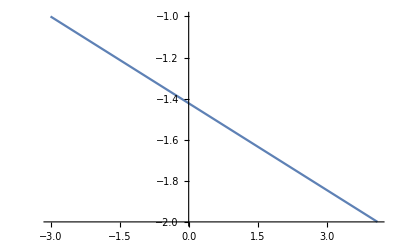

## Integrate descending pot

```mathematica
Clear[xL,xR,V0,ΔV];
V[x_,y_]:=V0 - ΔV*(x-xL)/(xR-xL);
Vint[Gx_,Gy_]:=Integrate[V[x,y]*Exp[ⅈ*(Gx*x+Gy*y)]/vol,{x,xL,xR},{y,yL,yR}];
Vint[0,0];
Vint[0,Gy];
Vint[Gx,0];
Vint[Gx,Gy]
Integrate[x*Exp[ⅈ*Gx*x],{x,xL,xR}];
```

-((ⅇ^(ⅈ Gy yL)-ⅇ^(ⅈ Gy yR)) (ⅇ^(ⅈ Gx xL) (Gx V0 (xL-xR)+ⅈ ΔV)-ⅇ^(ⅈ Gx xR) (Gx (xL-xR) (V0-ΔV)+ⅈ ΔV)))/(Gx^2 Gy vol (xL-xR))